## Usage

## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

## Function

```mathematica
Needs["ErrorBarPlots`"];
MyBootStrapForSpotError[spots_,spotcount_,times_,sampleSize_,repetitions_]:=Module[{a,b,c,errorBS,stdevsBS,meansBS,meanTimeBS,repTimes,myOut},
a = Table[Table[Table[RandomChoice[spots[[All,i]]],sampleSize],repetitions ],{i,1,Length@spotcount,1}];
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS ;
errorBS =ErrorBar/@stdevsBS;
b = Transpose[{spotcount ,errorBS}];
c = Table[times,repetitions]//Transpose;
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
myOut = {b,meanTimeBS}
]
```

## Generate global Har translation decay plots

### Reading In Parameters:

```mathematica
AALength=(4645+1010/2);
(* using 1717 AA because that's half of the smFLAG tag and the entire ORF of KDM5B*)
myStartTime=5;
myEndTime=65;
```

```mathematica
sampleSize = Length@onlyYellowSpots  ;
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 30  ;(* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

### Reading In Files

```mathematica
(*YOU WILL GET AN ERROR if you don't have a W, Y, G, and P file for each cell!!! *)
```

```mathematica
analysisFolder = "/Volumes/MINI/_har TEMP use for global analysis/"
```

/Volumes/MINI/_har TEMP use for global analysis/

```mathematica
myFolders = {"/Volumes/MINI/_har TEMP use for global analysis/20180910_Har/Analysis",     "/Volumes/MINI/_har TEMP use for global analysis/20180926_harringtonine_TL_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181024_har_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181026_TLhar/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181027_TL_same cells as overnight_HAR/Analysis" };
```

```mathematica
myYellowOnlyFiles = FileNames["*ySpotNTime.m",myFolders];
cellCount = Length@myYellowOnlyFiles
myNTYellowOnlyFiles = FileNames["*NT*ySpotNTime.m",myFolders];
NTcellCount = Length@myNTYellowOnlyFiles
myTLYellowOnlyFiles = FileNames["*TL*ySpotNTime.m",myFolders];
TLcellCount = Length@myTLYellowOnlyFiles
myTAYellowOnlyFiles = FileNames["*TA*ySpotNTime.m",myFolders];
TAcellCount = Length@myTAYellowOnlyFiles
```

21

5

5

11

```mathematica
myWhiteFiles =FileNames["*wSpotNTime.m",myFolders];
Length@myWhiteFiles
myTAWhiteFiles =FileNames["*TA*wSpotNTime.m",myFolders];
Length@myTAWhiteFiles
myNTWhiteFiles =FileNames["*NT*wSpotNTime.m",myFolders];
Length@myNTWhiteFiles
myTLWhiteFiles =FileNames["*TL*wSpotNTime.m",myFolders];
Length@myTLWhiteFiles
```

21

11

5

5

```mathematica
myAllYellowFiles = FileNames["*gSpotNTime.m",myFolders];
Length@myAllYellowFiles
myTAAllYellowFiles = FileNames["*TA*gSpotNTime.m",myFolders];
Length@myTAAllYellowFiles
myNTAllYellowFiles = FileNames["*NT*gSpotNTime.m",myFolders];
Length@myNTAllYellowFiles
myTLAllYellowFiles = FileNames["*TL*gSpotNTime.m",myFolders];
Length@myTLAllYellowFiles
```

21

11

5

5

```mathematica
myPurpleFiles = FileNames["*brSpotNTime.m",myFolders];
Length@myPurpleFiles
myTAPurpleFiles = FileNames["*TA*brSpotNTime.m",myFolders];
Length@myTAPurpleFiles
myNTPurpleFiles = FileNames["*NT*brSpotNTime.m",myFolders];
Length@myNTPurpleFiles
myTLPurpleFiles = FileNames["*TL*brSpotNTime.m",myFolders];
Length@myTLPurpleFiles
```

21

11

5

5

### Yellow Only Har translation decay

```mathematica
onlyYellow = Table[Import[myYellowOnlyFiles⟦j⟧],{j,1,Length@myYellowOnlyFiles,1}];
TAonlyYellow = Table[Import[myTAYellowOnlyFiles⟦j⟧],{j,1,Length@myTAYellowOnlyFiles,1}];
NTonlyYellow = Table[Import[myTLYellowOnlyFiles⟦j⟧],{j,1,Length@myTLYellowOnlyFiles,1}];
TLonlyYellow = Table[Import[myNTYellowOnlyFiles⟦j⟧],{j,1,Length@myNTYellowOnlyFiles,1}];
```

#### ALL :

```mathematica
name = "ALL";
spotCount = Total[Transpose[onlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[onlyYellow],{2}]//#[[All,1]]/cellCount&;
```

```mathematica
yelOnlySpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*);
```

{{-178,203},{-118,188},{-58,178},{2,166},{62,176},{122,193},{182,182},{242,173},{302,171},{362,152},{422,157},{482,153},{542,142},{602,134},{662,128},{722,118},{782,116},{842,124},{902,101},{962,103},{1022,104},{1082,95},{1142,103},{1202,83},{1262,88},{1322,86},{1382,78},{1442,81},{1502,82},{1562,73},{1622,69},{1682,68},{1742,76},{1802,65},{1862,57},{1922,55},{1982,64},{2042,51},{2102,50},{2162,48},{2222,50},{2282,42},{2342,54},{2402,48},{2462,39},{2522,50},{2582,33},{2642,32},{2702,40},{2762,31},{2822,31},{2882,38},{2942,33},{3002,30},{3062,30},{3122,28},{3182,27},{3242,32},{3302,28},{3362,25},{3422,28},{3482,25},{3542,30},{3602,33},{3662,20}}

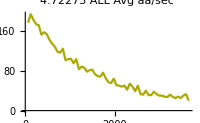
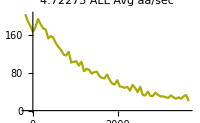
{{4.72273,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelOnlySpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec" name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec" name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

#### EXPORT “ALL”:

```mathematica
yelOnlyTime = spotTime;
Export[analysisFolder<>"_ALLyOnlyGlobalTimePlot.tif",yelOnlyTimePlot];
yelOnlySpotCount>>analysisFolder<>"_ALLOnlyGlobalTime.m"
```

#### TA:

```mathematica
name = "TA";
TAspotCount = Total[Transpose[TAonlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[TAonlyYellow],{2}]//#[[All,1]]/TAcellCount&;
```

```mathematica
TAyelOnlySpotCount= Transpose[{times,TAspotCount}](*Combining Time with the # of spots*);
```

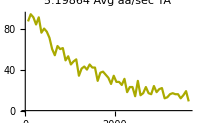
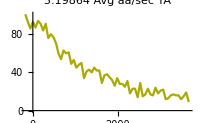
{{5.19864,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TAyelOnlySpotCount;
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TAyelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec" ), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_TAyOnlyGlobalTimePlot.tif",TAyelOnlyTimePlot];
TAyelOnlySpotCount>>analysisFolder<>"_TAOnlyGlobalTime.m"
```

#### NT:

```mathematica
name = "NT";
NTspotCount = Total[Transpose[NTonlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[NTonlyYellow],{2}]//#[[All,1]]/NTcellCount&;
```

```mathematica
NTyelOnlySpotCount= Transpose[{times,NTspotCount}](*Combining Time with the # of spots*);
```

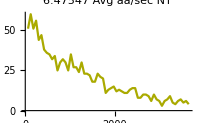
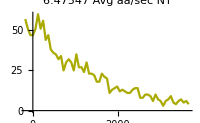
{{6.47547,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = NTyelOnlySpotCount;
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{NTyelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec" ), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_NTyOnlyGlobalTimePlot.tif",NTyelOnlyTimePlot];
NTyelOnlySpotCount>>analysisFolder<>"_NTOnlyGlobalTime.m"
```

#### TL:

```mathematica
name = "TL";
TLspotCount = Total[Transpose[TLonlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[TLonlyYellow],{2}]//#[[All,1]]/TLcellCount&;
```

```mathematica
TLyelOnlySpotCount= Transpose[{times,TLspotCount}](*Combining Time with the # of spots*);
```

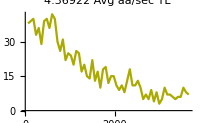
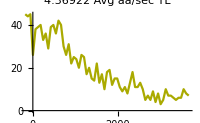
{{4.36922,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TLyelOnlySpotCount;
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TLyelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec" ), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
NTspotTime = spotTime;
Export[analysisFolder<>"_TLyOnlyGlobalTimePlot.tif",TLyelOnlyTimePlot];
TLyelOnlySpotCount>>analysisFolder<>"_TLOnlyGlobalTime.m"
```

### Yellow All Har translation decay

```mathematica
allYellow = Table[Import[myAllYellowFiles⟦j⟧],{j,1,Length@myAllYellowFiles,1}];
TAallYellow = Table[Import[myTAAllYellowFiles⟦j⟧],{j,1,Length@myTAAllYellowFiles,1}];
NTallYellow = Table[Import[myNTAllYellowFiles⟦j⟧],{j,1,Length@myNTAllYellowFiles,1}];
TLallYellow = Table[Import[myTLAllYellowFiles⟦j⟧],{j,1,Length@myTLAllYellowFiles,1}];
```

#### ALL:

```mathematica
name = "ALL";
spotCount = Total[Transpose[allYellow],{2}]//#[[All,2]]&;
```

```mathematica
yelAllSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*);
```

{{-178,277},{-118,267},{-58,246},{2,231},{62,245},{122,251},{182,264},{242,237},{302,238},{362,220},{422,211},{482,205},{542,197},{602,188},{662,169},{722,176},{782,164},{842,165},{902,144},{962,153},{1022,143},{1082,130},{1142,141},{1202,121},{1262,128},{1322,127},{1382,123},{1442,113},{1502,120},{1562,113},{1622,105},{1682,108},{1742,117},{1802,91},{1862,87},{1922,90},{1982,92},{2042,82},{2102,71},{2162,70},{2222,67},{2282,67},{2342,73},{2402,72},{2462,59},{2522,69},{2582,53},{2642,56},{2702,54},{2762,46},{2822,48},{2882,46},{2942,43},{3002,47},{3062,39},{3122,36},{3182,36},{3242,42},{3302,41},{3362,32},{3422,34},{3482,34},{3542,38},{3602,42},{3662,30}}

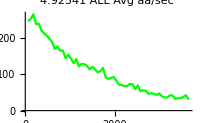
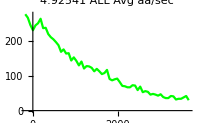
{{4.92541,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
yelAllTime = spotTime;
Export[analysisFolder<>"_ALLyAllGlobalTimePlot.tif",yelAllTimePlot];
yelAllSpotCount>>analysisFolder<>"_ALLyAllGlobalTime.m"
```

#### TA:

```mathematica
name = "TA";
TAspotCount = Total[Transpose[TAallYellow],{2}]//#[[All,2]]&;
```

```mathematica
TAyelAllSpotCount= Transpose[{times,TAspotCount}](*Combining Time with the # of spots*);
```

{{-178,146},{-118,139},{-58,123},{2,128},{62,125},{122,127},{182,137},{242,120},{302,129},{362,117},{422,113},{482,109},{542,104},{602,92},{662,80},{722,101},{782,90},{842,85},{902,75},{962,86},{1022,70},{1082,72},{1142,73},{1202,55},{1262,66},{1322,70},{1382,68},{1442,62},{1502,64},{1562,67},{1622,56},{1682,64},{1742,66},{1802,51},{1862,53},{1922,52},{1982,54},{2042,48},{2102,42},{2162,41},{2222,40},{2282,33},{2342,32},{2402,38},{2462,29},{2522,40},{2582,30},{2642,34},{2702,32},{2762,29},{2822,25},{2882,30},{2942,24},{3002,32},{3062,28},{3122,17},{3182,19},{3242,22},{3302,25},{3362,20},{3422,18},{3482,18},{3542,19},{3602,25},{3662,16}}

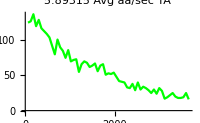
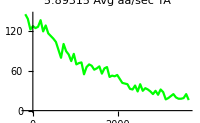
{{5.89315,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TAyelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TAyelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_TAyAllGlobalTimePlot.tif",TAyelAllTimePlot];
TAyelAllSpotCount>>analysisFolder<>"_TAyAllGlobalTime.m"
```

#### TL:

```mathematica
name = "TL";
TLspotCount = Total[Transpose[TLallYellow],{2}]//#[[All,2]]&;
```

```mathematica
TLyelAllSpotCount= Transpose[{times,TLspotCount}](*Combining Time with the # of spots*);
```

{{-178,86},{-118,84},{-58,78},{2,77},{62,82},{122,85},{182,87},{242,84},{302,73},{362,74},{422,59},{482,56},{542,57},{602,54},{662,49},{722,45},{782,48},{842,49},{902,47},{962,42},{1022,49},{1082,38},{1142,42},{1202,41},{1262,45},{1322,37},{1382,40},{1442,37},{1502,34},{1562,33},{1622,32},{1682,34},{1742,33},{1802,21},{1862,22},{1922,23},{1982,23},{2042,23},{2102,20},{2162,18},{2222,19},{2282,21},{2342,23},{2402,23},{2462,19},{2522,16},{2582,13},{2642,17},{2702,15},{2762,12},{2822,14},{2882,12},{2942,11},{3002,12},{3062,6},{3122,9},{3182,10},{3242,13},{3302,10},{3362,7},{3422,10},{3482,10},{3542,9},{3602,9},{3662,7}}

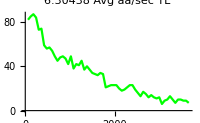
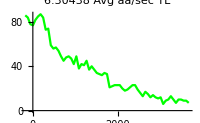
{{6.30438,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TLyelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TLyelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_TLyAllGlobalTimePlot.tif",TLyelAllTimePlot];
TLyelAllSpotCount>>analysisFolder<>"_TLyAllGlobalTime.m"
```

#### NT:

```mathematica
name = "NT";
NTspotCount = Total[Transpose[NTallYellow],{2}]//#[[All,2]]&;
```

```mathematica
NTyelAllSpotCount= Transpose[{times,NTspotCount}](*Combining Time with the # of spots*)
```

{{-178,45},{-118,44},{-58,45},{2,26},{62,38},{122,39},{182,40},{242,33},{302,36},{362,29},{422,39},{482,40},{542,36},{602,42},{662,40},{722,30},{782,26},{842,31},{902,22},{962,25},{1022,24},{1082,20},{1142,26},{1202,25},{1262,17},{1322,20},{1382,15},{1442,14},{1502,22},{1562,13},{1622,17},{1682,10},{1742,18},{1802,19},{1862,12},{1922,15},{1982,15},{2042,11},{2102,9},{2162,11},{2222,8},{2282,13},{2342,18},{2402,11},{2462,11},{2522,13},{2582,10},{2642,5},{2702,7},{2762,5},{2822,9},{2882,4},{2942,8},{3002,3},{3062,5},{3122,10},{3182,7},{3242,7},{3302,6},{3362,5},{3422,6},{3482,6},{3542,10},{3602,8},{3662,7}}

{{-178,45},{-118,44},{-58,45},{2,26},{62,38},{122,39},{182,40},{242,33},{302,36},{362,29},{422,39},{482,40},{542,36},{602,42},{662,40},{722,30},{782,26},{842,31},{902,22},{962,25},{1022,24},{1082,20},{1142,26},{1202,25},{1262,17},{1322,20},{1382,15},{1442,14},{1502,22},{1562,13},{1622,17},{1682,10},{1742,18},{1802,19},{1862,12},{1922,15},{1982,15},{2042,11},{2102,9},{2162,11},{2222,8},{2282,13},{2342,18},{2402,11},{2462,11},{2522,13},{2582,10},{2642,5},{2702,7},{2762,5},{2822,9},{2882,4},{2942,8},{3002,3},{3062,5},{3122,10},{3182,7},{3242,7},{3302,6},{3362,5},{3422,6},{3482,6},{3542,10},{3602,8},{3662,7}}

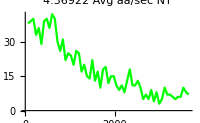
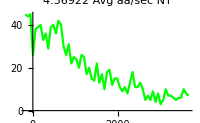
{{4.36922,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = NTyelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{NTyelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_NTyAllGlobalTimePlot.tif",NTyelAllTimePlot];
NTyelAllSpotCount>>analysisFolder<>"_NTyAllGlobalTime.m"
```

### White Har translation decay

```mathematica
white = Table[Import[myWhiteFiles⟦j⟧],{j,1,Length@myWhiteFiles,1}];
NTwhite = Table[Import[myNTWhiteFiles⟦j⟧],{j,1,Length@myNTWhiteFiles,1}];
TAwhite = Table[Import[myTAWhiteFiles⟦j⟧],{j,1,Length@myTAWhiteFiles,1}];
TLwhite = Table[Import[myTLWhiteFiles⟦j⟧],{j,1,Length@myTLWhiteFiles,1}];
```

#### ALL:

```mathematica
spotCount = Total[Transpose[white],{2}]//#[[All,2]]&;
times = Total[Transpose[white],{2}]//#[[All,1]]/cellCount&;
whiteSpotCount= Transpose[{times,spotCount}];(*Combining Time with the # of spots*)
```

{{-178,74},{-118,79},{-58,68},{2,65},{62,69},{122,58},{182,82},{242,64},{302,67},{362,68},{422,54},{482,52},{542,55},{602,54},{662,41},{722,58},{782,48},{842,41},{902,43},{962,50},{1022,39},{1082,35},{1142,38},{1202,38},{1262,40},{1322,41},{1382,45},{1442,32},{1502,38},{1562,40},{1622,36},{1682,40},{1742,41},{1802,26},{1862,30},{1922,35},{1982,28},{2042,31},{2102,21},{2162,22},{2222,17},{2282,25},{2342,19},{2402,24},{2462,20},{2522,19},{2582,20},{2642,24},{2702,14},{2762,15},{2822,17},{2882,8},{2942,10},{3002,17},{3062,9},{3122,8},{3182,9},{3242,10},{3302,13},{3362,7},{3422,6},{3482,9},{3542,8},{3602,9},{3662,10}}

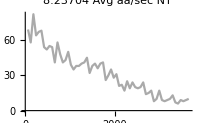
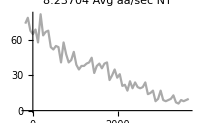
{{8.23704,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = whiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{whiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
whiteAllTime = spotTime;
Export[analysisFolder<>"_ALLwGlobalTimePlot.tif",whiteTimePlot];
whiteSpotCount>>analysisFolder<>"_ALLwGlobalTime.m"
```

#### TA:

```mathematica
TAspotCount = Total[Transpose[TAwhite],{2}]//#[[All,2]]&;
```

```mathematica
name  = "TA";
TAwhiteSpotCount= Transpose[{times,TAspotCount}];(*Combining Time with the # of spots*)
```

{{-178,74},{-118,79},{-58,68},{2,65},{62,69},{122,58},{182,82},{242,64},{302,67},{362,68},{422,54},{482,52},{542,55},{602,54},{662,41},{722,58},{782,48},{842,41},{902,43},{962,50},{1022,39},{1082,35},{1142,38},{1202,38},{1262,40},{1322,41},{1382,45},{1442,32},{1502,38},{1562,40},{1622,36},{1682,40},{1742,41},{1802,26},{1862,30},{1922,35},{1982,28},{2042,31},{2102,21},{2162,22},{2222,17},{2282,25},{2342,19},{2402,24},{2462,20},{2522,19},{2582,20},{2642,24},{2702,14},{2762,15},{2822,17},{2882,8},{2942,10},{3002,17},{3062,9},{3122,8},{3182,9},{3242,10},{3302,13},{3362,7},{3422,6},{3482,9},{3542,8},{3602,9},{3662,10}}

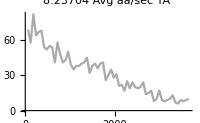
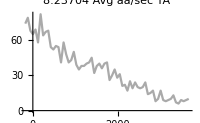
{{8.23704,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = whiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TAwhiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_TAwGlobalTimePlot.tif",TAwhiteTimePlot];
TAwhiteSpotCount>>analysisFolder<>"_TAwGlobalTime.m"
```

#### TL:

```mathematica
TLspotCount = Total[Transpose[TLwhite],{2}]//#[[All,2]]&;
```

```mathematica
name  = "TL";
TLwhiteSpotCount= Transpose[{times,TLspotCount}];(*Combining Time with the # of spots*)
```

{{-178,29},{-118,33},{-58,31},{2,30},{62,31},{122,25},{182,36},{242,28},{302,29},{362,27},{422,21},{482,20},{542,22},{602,22},{662,15},{722,20},{782,18},{842,17},{902,17},{962,17},{1022,14},{1082,11},{1142,15},{1202,17},{1262,15},{1322,14},{1382,17},{1442,15},{1502,16},{1562,15},{1622,9},{1682,13},{1742,13},{1802,10},{1862,9},{1922,9},{1982,8},{2042,11},{2102,7},{2162,6},{2222,8},{2282,10},{2342,10},{2402,9},{2462,5},{2522,8},{2582,5},{2642,7},{2702,5},{2762,3},{2822,8},{2882,2},{2942,4},{3002,6},{3062,3},{3122,3},{3182,3},{3242,4},{3302,5},{3362,3},{3422,4},{3482,3},{3542,4},{3602,3},{3662,3}}

Part::partd: Part specification {{-178,29},{-118,33},{-58,31},{2,30},{62,31},{122,25},{182,36},{242,28},{302,29},{362,27},{422,21},{482,20},{542,22},{602,22},{662,15},{722,20},{782,18},{842,17},{902,17},{962,17},{1022,14},{1082,11},{1142,15},{1202,17},{1262,15},{1322,14},{1382,17},{1442,15},{1502,16},{1562,15},{1622,9},{1682,13},{1742,13},{1802,10},{1862,9},{1922,9},{1982,8},{2042,11},{2102,7},{2162,6},{2222,8},{2282,10},{2342,10},{2402,9},{2462,5},{2522,8},{2582,5},{2642,7},{2702,5},{2762,3},«15»}⟦0,2⟧ is longer than depth of object.

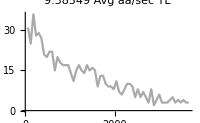
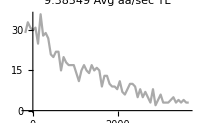
{{9.38549,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TLwhiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TLwhiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_TLwGlobalTimePlot.tif",TLwhiteTimePlot];
TLwhiteSpotCount>>analysisFolder<>"_TLwGlobalTime.m"
```

#### NT:

```mathematica
name  = "NT";
NTspotCount = Total[Transpose[NTwhite],{2}]//#[[All,2]]&
NTwhiteSpotCount= Transpose[{times,NTspotCount}](*Combining Time with the # of spots*)
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{-178,0},{-118,0},{-58,0},{2,0},{62,0},{122,0},{182,0},{242,0},{302,0},{362,0},{422,0},{482,0},{542,0},{602,0},{662,0},{722,0},{782,0},{842,0},{902,0},{962,0},{1022,0},{1082,0},{1142,0},{1202,0},{1262,0},{1322,0},{1382,0},{1442,0},{1502,0},{1562,0},{1622,0},{1682,0},{1742,0},{1802,0},{1862,0},{1922,0},{1982,0},{2042,0},{2102,0},{2162,0},{2222,0},{2282,0},{2342,0},{2402,0},{2462,0},{2522,0},{2582,0},{2642,0},{2702,0},{2762,0},{2822,0},{2882,0},{2942,0},{3002,0},{3062,0},{3122,0},{3182,0},{3242,0},{3302,0},{3362,0},{3422,0},{3482,0},{3542,0},{3602,0},{3662,0}}

{{-178,0},{-118,0},{-58,0},{2,0},{62,0},{122,0},{182,0},{242,0},{302,0},{362,0},{422,0},{482,0},{542,0},{602,0},{662,0},{722,0},{782,0},{842,0},{902,0},{962,0},{1022,0},{1082,0},{1142,0},{1202,0},{1262,0},{1322,0},{1382,0},{1442,0},{1502,0},{1562,0},{1622,0},{1682,0},{1742,0},{1802,0},{1862,0},{1922,0},{1982,0},{2042,0},{2102,0},{2162,0},{2222,0},{2282,0},{2342,0},{2402,0},{2462,0},{2522,0},{2582,0},{2642,0},{2702,0},{2762,0},{2822,0},{2882,0},{2942,0},{3002,0},{3062,0},{3122,0},{3182,0},{3242,0},{3302,0},{3362,0},{3422,0},{3482,0},{3542,0},{3602,0},{3662,0}}

Part::partd: Part specification {{-178,0},{-118,0},{-58,0},{2,0},{62,0},{122,0},{182,0},{242,0},{302,0},{362,0},{422,0},{482,0},{542,0},{602,0},{662,0},{722,0},{782,0},{842,0},{902,0},{962,0},{1022,0},{1082,0},{1142,0},{1202,0},{1262,0},{1322,0},{1382,0},{1442,0},{1502,0},{1562,0},{1622,0},{1682,0},{1742,0},{1802,0},{1862,0},{1922,0},{1982,0},{2042,0},{2102,0},{2162,0},{2222,0},{2282,0},{2342,0},{2402,0},{2462,0},{2522,0},{2582,0},{2642,0},{2702,0},{2762,0},«15»}⟦0,2⟧ is longer than depth of object.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

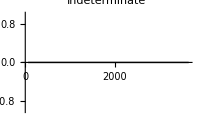
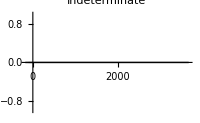
{{Indeterminate,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = NTwhiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{NTwhiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_NTwGlobalTimePlot.tif",NTwhiteTimePlot];
NTwhiteSpotCount>>analysisFolder<>"_NTwGlobalTime.m"
```

### Purple Har translation decay

```mathematica
purple = Table[Import[myPurpleFiles⟦j⟧],{j,1,Length@myPurpleFiles,1}];
TApurple = Table[Import[myTAPurpleFiles⟦j⟧],{j,1,Length@myTAPurpleFiles,1}];
TLpurple = Table[Import[myTLPurpleFiles⟦j⟧],{j,1,Length@myTLPurpleFiles,1}];
NTpurple = Table[Import[myNTPurpleFiles⟦j⟧],{j,1,Length@myNTPurpleFiles,1}];
```

#### ALL:

```mathematica
name = "ALL";
spotCount = Total[Transpose[purple],{2}]//#[[All,2]]&;
purpleSpotCount= Transpose[{times,spotCount}];(*Combining Time with the # of spots*)
```

{{-178,297},{-118,296},{-58,270},{2,264},{62,290},{122,281},{182,288},{242,282},{302,278},{362,277},{422,266},{482,280},{542,260},{602,277},{662,278},{722,282},{782,276},{842,263},{902,279},{962,258},{1022,254},{1082,265},{1142,255},{1202,256},{1262,264},{1322,255},{1382,273},{1442,261},{1502,281},{1562,262},{1622,257},{1682,252},{1742,253},{1802,237},{1862,230},{1922,227},{1982,252},{2042,248},{2102,242},{2162,243},{2222,219},{2282,264},{2342,247},{2402,242},{2462,217},{2522,250},{2582,235},{2642,247},{2702,234},{2762,233},{2822,242},{2882,230},{2942,221},{3002,242},{3062,248},{3122,244},{3182,234},{3242,224},{3302,222},{3362,228},{3422,248},{3482,238},{3542,227},{3602,219},{3662,238}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

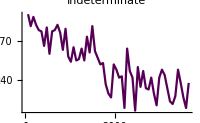
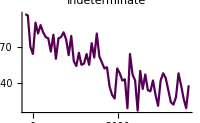
{{Indeterminate,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = purpleSpotCount
purpleSpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{purpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
purpleAllTime = spotTime;
Export[analysisFolder<>"_ALLpGlobalTimePlot.tif",purpleTimePlot];
purpleSpotCount>>analysisFolder<>"_ALLpGlobalTime.m"
```

#### TA:

```mathematica
name = "TA";
TAspotCount = Total[Transpose[TApurple],{2}]//#[[All,2]]&;
TApurpleSpotCount= Transpose[{times,TAspotCount}];(*Combining Time with the # of spots*)
```

{{-178,207},{-118,212},{-58,192},{2,187},{62,201},{122,209},{182,205},{242,206},{302,193},{362,200},{422,197},{482,211},{542,195},{602,193},{662,210},{722,199},{782,208},{842,191},{902,207},{962,194},{1022,182},{1082,197},{1142,185},{1202,188},{1262,189},{1322,189},{1382,194},{1442,194},{1502,211},{1562,188},{1622,190},{1682,181},{1742,184},{1802,172},{1862,171},{1922,166},{1982,185},{2042,187},{2102,181},{2162,174},{2222,163},{2282,192},{2342,182},{2402,182},{2462,167},{2522,189},{2582,182},{2642,192},{2702,171},{2762,169},{2822,181},{2882,164},{2942,173},{3002,199},{3062,188},{3122,187},{3182,183},{3242,168},{3302,168},{3362,173},{3422,191},{3482,184},{3542,176},{3602,171},{3662,188}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

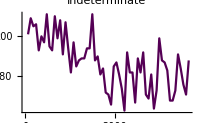
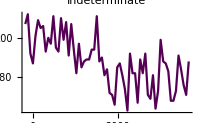
{{Indeterminate,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TApurpleSpotCount
purpleSpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TApurpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_TApGlobalTimePlot.tif",TApurpleTimePlot];
TApurpleSpotCount>>analysisFolder<>"_TApGlobalTime.m"
```

#### TL:

```mathematica
name = "TL";
TLspotCount = Total[Transpose[TLpurple],{2}]//#[[All,2]]&;
TLpurpleSpotCount= Transpose[{times,TLspotCount}];(*Combining Time with the # of spots*)
```

{{-178,84},{-118,82},{-58,77},{2,74},{62,86},{122,70},{182,82},{242,75},{302,84},{362,77},{422,66},{482,68},{542,62},{602,82},{662,68},{722,82},{782,65},{842,71},{902,71},{962,63},{1022,70},{1082,66},{1142,70},{1202,68},{1262,74},{1322,65},{1382,79},{1442,67},{1502,70},{1562,74},{1622,67},{1682,68},{1742,69},{1802,64},{1862,58},{1922,60},{1982,67},{2042,61},{2102,61},{2162,69},{2222,55},{2282,72},{2342,65},{2402,60},{2462,50},{2522,61},{2582,52},{2642,55},{2702,62},{2762,63},{2822,61},{2882,66},{2942,48},{3002,43},{3062,60},{3122,57},{3182,51},{3242,56},{3302,54},{3362,55},{3422,57},{3482,53},{3542,51},{3602,48},{3662,50}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

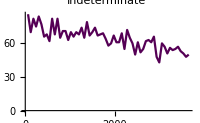
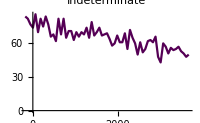
{{Indeterminate,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TLpurpleSpotCount
purpleSpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TLpurpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_TLpGlobalTimePlot.tif",TLpurpleTimePlot];
TLpurpleSpotCount>>analysisFolder<>"_TLpGlobalTime.m"
```

#### NT:

```mathematica
name = "NT";
spotCount = Total[Transpose[NTpurple],{2}]//#[[All,2]]&;
NTpurpleSpotCount= Transpose[{times,spotCount}];(*Combining Time with the # of spots*)
```

{{-178,6},{-118,2},{-58,1},{2,3},{62,3},{122,2},{182,1},{242,1},{302,1},{362,0},{422,3},{482,1},{542,3},{602,2},{662,0},{722,1},{782,3},{842,1},{902,1},{962,1},{1022,2},{1082,2},{1142,0},{1202,0},{1262,1},{1322,1},{1382,0},{1442,0},{1502,0},{1562,0},{1622,0},{1682,3},{1742,0},{1802,1},{1862,1},{1922,1},{1982,0},{2042,0},{2102,0},{2162,0},{2222,1},{2282,0},{2342,0},{2402,0},{2462,0},{2522,0},{2582,1},{2642,0},{2702,1},{2762,1},{2822,0},{2882,0},{2942,0},{3002,0},{3062,0},{3122,0},{3182,0},{3242,0},{3302,0},{3362,0},{3422,0},{3482,1},{3542,0},{3602,0},{3662,0}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

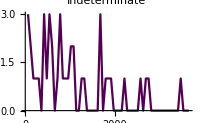
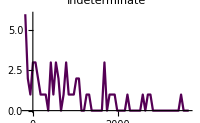
{{Indeterminate,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = NTpurpleSpotCount
purpleSpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{NTpurpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_NTpGlobalTimePlot.tif",NTpurpleTimePlot];
NTpurpleSpotCount>>analysisFolder<>"_NTpGlobalTime.m"
```

### View it all...

```mathematica
Row[{"All cells"}]
Row[{purpleTimePlot,whiteTimePlot,yelOnlyTimePlot,yelAllTimePlot}]
```

All cells

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{"TA cells"}]
Row[{TApurpleTimePlot,TAwhiteTimePlot,TAyelOnlyTimePlot,TAyelAllTimePlot}]
```

TA cells

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{"TL cells"}]
Row[{TLpurpleTimePlot,TLwhiteTimePlot,TLyelOnlyTimePlot,TLyelAllTimePlot}]
```

TL cells

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{"NT cells"}]
Row[{NTpurpleTimePlot,NTwhiteTimePlot,NTyelOnlyTimePlot,NTyelAllTimePlot}]
```

NT cells

-Graphics--Graphics--Graphics--Graphics-

## Bootstrapping the datasets:

### Reading In BS Parameters:

```mathematica
sampleSize = TAcellCount
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 30  (* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

11

30

### BS for Only Yellow Spots:

### ALL: BS for Only Yellow Spots:

```mathematica
onlyYellow0 = onlyYellow[[All,All,2]];
```

```mathematica
myBS = MyBootStrapForSpotError[onlyYellow0,yelOnlySpotCount,yelAllTime,times,sampleSize,repetitions];
```

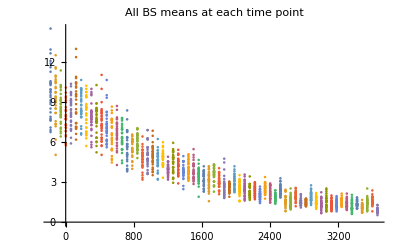

```mathematica
myBS[[2]]//ListPlot[
#,PlotLabel->"All BS means at each time point"]&
```

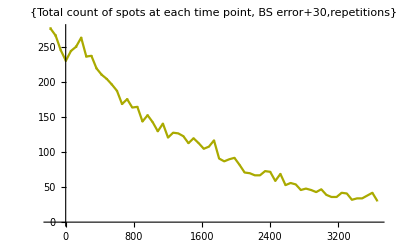

```mathematica
myBS[[1]]//ErrorListPlot[#,PlotStyle->{Darker[Yellow]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True,PlotRange->{0,All}]&
```

### NT: BS for Only Yellow Spots:

```mathematica
onlyYellow0 = NTonlyYellow[[All,All,2]];
```

```mathematica
myBS = MyBootStrapForSpotError[onlyYellow0,NTyelOnlySpotCount,times,sampleSize,repetitions];
```

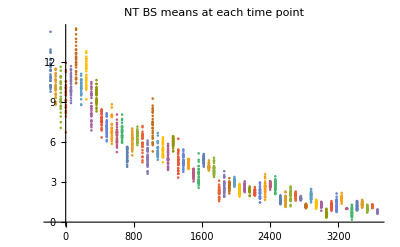

```mathematica
myBS[[2]]//ListPlot[
#,PlotLabel->"NT BS means at each time point"]&
```

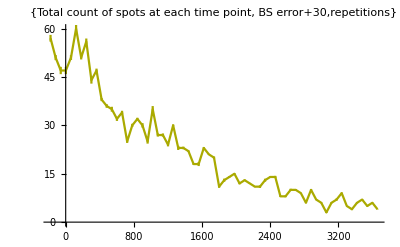

```mathematica
myBS[[1]]//ErrorListPlot[#,PlotStyle->{Darker[Yellow]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True,PlotRange->{0,All}]&
```

### TL: BS for Only Yellow Spots:

```mathematica
onlyYellow0 = TLonlyYellow[[All,All,2]];
```

```mathematica
myBS = MyBootStrapForSpotError[onlyYellow0,TLyelOnlySpotCount,times,sampleSize,repetitions];
```

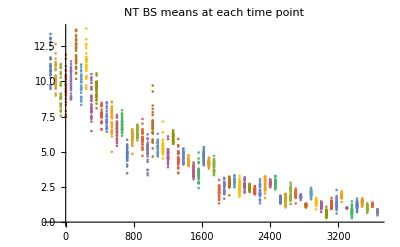

```mathematica
myBS[[2]]//ListPlot[
#,PlotLabel->"TL BS means at each time point"]&
```

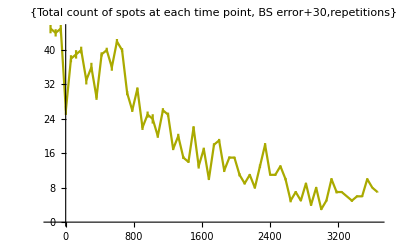

```mathematica
myBS[[1]]//ErrorListPlot[#,PlotStyle->{Darker[Yellow]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True,PlotRange->{0,All}]&
```

### TA: BS for Only Yellow Spots:

```mathematica
onlyYellow0 = TAonlyYellow[[All,All,2]];
```

```mathematica
myBS = MyBootStrapForSpotError[onlyYellow0,TAyelOnlySpotCount,times,sampleSize,repetitions];
```

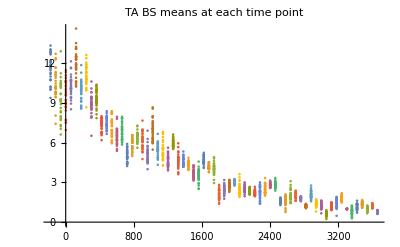

```mathematica
myBS[[2]]//ListPlot[
#,PlotLabel->"TA BS means at each time point"]&
```

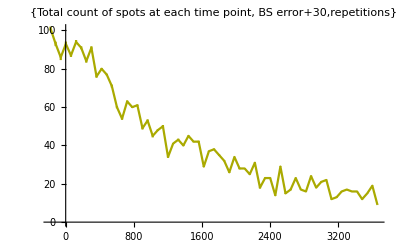

```mathematica
myBS[[1]]//ErrorListPlot[#,PlotStyle->{Darker[Yellow]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True,PlotRange->{0,All}]&
```

### BS for Purple Spots:

```mathematica
purple0 = purple[[All,All,2]];
```

```mathematica
myBS = MyBootStrapForSpotError[purple0,purpleSpotCount,purpleAllTime,times,sampleSize,repetitions];
```

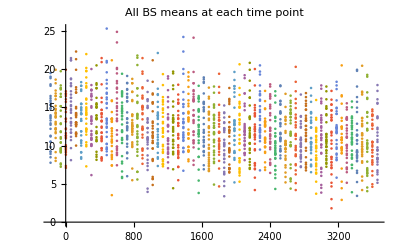

```mathematica
myBS[[2]]//ListPlot[
#,PlotLabel->"All BS means at each time point"]&
```

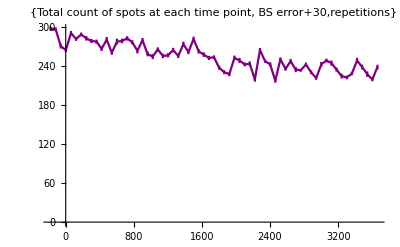

```mathematica
myBS[[1]]//ErrorListPlot[#,PlotStyle->{Purple}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True,PlotRange->{0,All}]&
```

### BS for White Spots:

```mathematica
white//Dimensions
```

{21,65,2}

```mathematica
white0 = white[[All,All,2]];
white0;
```

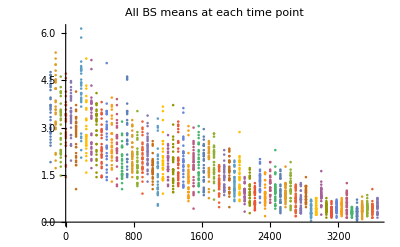

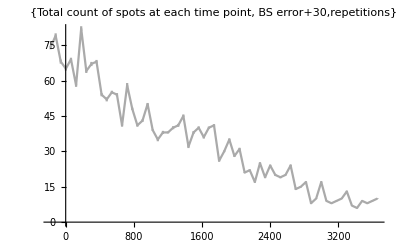

```mathematica
myBS = MyBootStrapForSpotError[white0,whiteSpotCount,whiteAllTime,times,sampleSize,repetitions];
myBS[[2]]//ListPlot[#
,PlotLabel->"All BS means at each time point"]&
myBS[[1]]//ErrorListPlot[#,PlotStyle->{Darker[White]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True,PlotRange->{0,All}]&
```

## OLD

### BS for Only Yellow Spots:

```mathematica
onlyYellowSpots = onlyYellow[[All,All,2]];
onlyYellowSpots;
```

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[onlyYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@yelOnlySpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS ;
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{11.1818,8.,13.7273,9.54545,10.4545,7.,8.63636,9.36364,10.2727,8.09091,9.36364,7.81818,11.8182,8.09091,10.9091,9.72727,8.45455,11.3636,11.9091,10.9091,10.4545,9.18182,7.72727,9.72727,9.18182,6.45455,8.,10.0909,5.18182,7.}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{yelOnlyTime ,errorBS}];
```

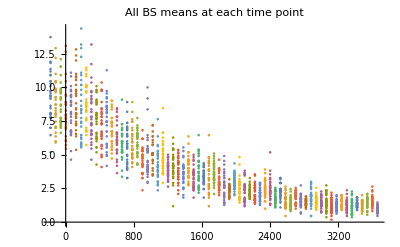

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

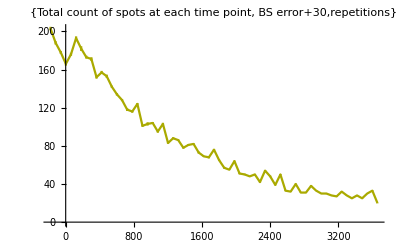

```mathematica
ErrorListPlot[b,PlotStyle->{Darker[Yellow]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True,PlotRange->{0,All}]
```

### BS for All Yellow Spots:

```mathematica
allYellow//Dimensions
```

{21,65,2}

```mathematica
allYellowSpots = allYellow[[All,All,2]];
allYellowSpots;
```

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[allYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@yelAllSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{2.45013,2.84194,1.99697,2.51811,2.06348,1.99343,2.07685,2.4307,2.23406,1.70523,2.0797,2.12742,1.35097,2.10642,1.18072,1.9259,1.57177,0.965265,1.50025,1.51353,1.35991,1.50341,1.64652,0.980168,1.70359,1.51048,1.17776,1.26129,1.41757,1.31185,0.940341,1.02845,1.31196,0.982704,0.883893,1.14339,0.738523,1.01384,0.787694,0.943769,0.804123,0.63123,0.889251,0.701638,0.765356,0.841144,0.603094,0.855167,0.989932,0.476881,0.50509,0.593976,0.516324,0.73968,0.61599,0.450705,0.452146,0.441086,0.733023,0.48145,0.390638,0.373952,0.613486,0.485175,0.474925}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{8.90909,11.0909,14.0909,11.2727,15.,13.4545,13.0909,15.,9.18182,14.6364,13.3636,18.1818,16.7273,13.0909,14.1818,11.4545,12.5455,9.45455,11.5455,11.2727,15.,12.6364,12.8182,14.,12.1818,11.4545,11.5455,9.27273,16.6364,17.9091}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{yelAllTime ,errorBS}];
```

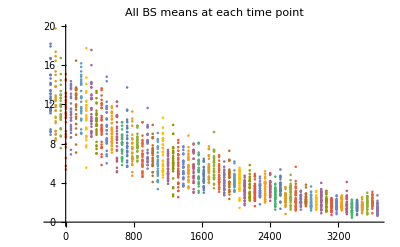

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

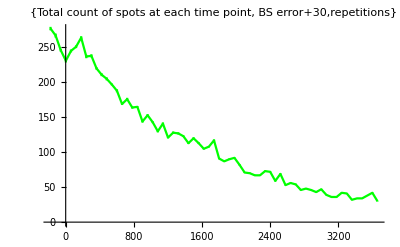

```mathematica
ErrorListPlot[b,PlotStyle->{Green}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True,PlotRange->{0,All}]
```

### BS for White Spots:

```mathematica
white//Dimensions
```

{21,65,2}

```mathematica
white0 = white[[All,All,2]];
white0;
```

```mathematica
a = Table[Table[Table[RandomChoice[white0[[All,i]]],sampleSize],repetitions ],{i,1,Length@whiteSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{whiteAllTime ,errorBS}];
```

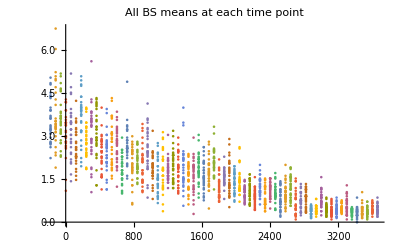

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

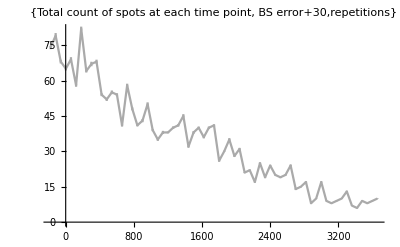

```mathematica
ErrorListPlot[b,PlotStyle->{Darker[White]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True,PlotRange->{0,All}]
```